## Bose-Hubbard model simulation

References:
	F. Verstraete, V. Murg, J. I. Cirac
	Matrix product states, projected entangled pair states, and variational renormalization group methods for quantum spin systems
	Advances in Physics 57, 143-224 (2008) DOI

	Thomas Barthel
	Precise evaluation of thermal response functions by optimized density matrix renormalization group schemes
	New Journal of Physics 15, 073010 (2013) DOI

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
SparseIdentityMatrix[d_]:=SparseArray[{i_,i_}->1,{d,d}]
```

```mathematica
SiteCreateOp[M_]:=DiagonalMatrix[Sqrt[Range[1,M]],-1]
SiteAnnihilOp[M_]:=DiagonalMatrix[Sqrt[Range[1,M]],1]
```

```mathematica
NumberOp[M_]:=DiagonalMatrix[Range[0,M]]
```

```mathematica
(* construct Bose-Hamiltonian with open boundary conditions *)
HBose[t_,U_,μ_,M_,1]:=U/2 NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1])-μ NumberOp[M]
HBose[t_,U_,μ_,M_,L_]:=-t Sum[KroneckerProduct[SparseIdentityMatrix[(M+1)^(j-1)],SiteCreateOp[M],SiteAnnihilOp[M],SparseIdentityMatrix[(M+1)^(L-j-1)]]+KroneckerProduct[SparseIdentityMatrix[(M+1)^(j-1)],SiteAnnihilOp[M],SiteCreateOp[M],SparseIdentityMatrix[(M+1)^(L-j-1)]],{j,1,L-1}]+Sum[KroneckerProduct[SparseIdentityMatrix[(M+1)^(j-1)],U/2 NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1])-μ NumberOp[M],SparseIdentityMatrix[(M+1)^(L-j)]],{j,1,L}]
```

### Simulation parameters

```mathematica
(* kinetic hopping parameter *)
Subscript[tH, val]=1;
```

```mathematica
(* interaction strength *)
Subscript[U, val]=5;
```

```mathematica
(* chemical potential *)
Subscript[μ, val]=1/7;
```

```mathematica
(* number of lattice sites *)
Subscript[L, val]=5;
```

```mathematica
(* single site occupation number cut-off *)
Subscript[M, val]=2;
```

```mathematica
(* inverse temperature *)
Subscript[β, val]=3/5;
```

```mathematica
Subscript[t, list]=Range[0,5,1/4];
Length[%]
```

21

### Out-of-time-order correlations

```mathematica
OperatorAverage[A_,H_,β_]:=Module[{expβH=MatrixExp[-β H]},Tr[expβH.A]/Tr[expβH]]
```

```mathematica
GF[A_,B_,H_,β_,t_]:=Module[{expβH=MatrixExp[-β H],At=MatrixExp[-ⅈ t H].A.MatrixExp[ⅈ t H]},Tr[expβH.At.B]/Tr[expβH]]
```

```mathematica
SiteCreateOpFull[j_,M_,L_]:=KroneckerProduct[SparseIdentityMatrix[(M+1)^j],SiteCreateOp[M],SparseIdentityMatrix[(M+1)^(L-j-1)]]
```

```mathematica
SiteAnnihilOpFull[j_,M_,L_]:=KroneckerProduct[SparseIdentityMatrix[(M+1)^j],SiteAnnihilOp[M],SparseIdentityMatrix[(M+1)^(L-j-1)]]
```

```mathematica
SiteNumberOpFull[j_,M_,L_]:=KroneckerProduct[SparseIdentityMatrix[(M+1)^j],NumberOp[M],SparseIdentityMatrix[(M+1)^(L-j-1)]]
```

```mathematica
Subscript[fn, import]="../output/bose_hubbard/L"<>ToString[Subscript[L, val]]<>"_hole/bose_hubbard_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]];
```

```mathematica
(* read simulation results from disk *)
```

```mathematica
Subscript[gfhole, list]=Import[Subscript[fn, import]<>"_gfhole.dat","Complex128"];
Dimensions[%]
```

{21}

```mathematica
Subscript[i, site]=1;
Subscript[j, site]=3;
```

```mathematica
(* reference calculation *)
```

```mathematica
Block[{tH=Subscript[tH, val],U=Subscript[U, val],μ=Subscript[μ, val],M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],HB},HB=N[HBose[tH,U,μ,M,L]];Subscript[gfhole, list,ref]=Table[GF[SiteAnnihilOpFull[L-Subscript[i, site]-1,M,L],SiteCreateOpFull[L-Subscript[j, site]-1,M,L],HB,β,t],{t,Subscript[t, list]}]];
```

```mathematica
Dimensions[Subscript[gfhole, list,ref]]
```

{21}

```mathematica
(* compare *)
Norm[Subscript[gfhole, list]-Subscript[gfhole, list,ref],∞]
```

0.0000289166

```mathematica
Subscript[plot, label]="Bose-Hubbard model with\nt_H="<>ToString[Subscript[tH, val]]<>", U="<>ToString[Subscript[U, val]]<>", μ="<>ToString[InputForm[Subscript[μ, val]]]<>", M="<>ToString[Subscript[M, val]]<>", L="<>ToString[Subscript[L, val]]<>", β="<>ToString[N[Subscript[β, val]]]<>"\nsites: i="<>ToString[Subscript[i, site]]<>", j="<>ToString[Subscript[j, site]];
```

```mathematica
Subscript[fn, export]="plots/"<>#<>"/"<>#<>"_"&[FileBaseName[NotebookFileName[]]];
```

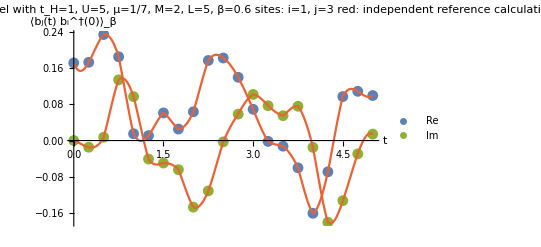

```mathematica
Show[ListPlot[{Transpose[{Subscript[t, list],Re[Subscript[gfhole, list]]}],Transpose[{Subscript[t, list],Im[Subscript[gfhole, list]]}]},AxesLabel->{"t","⟨b_j(t) b_i^†(0)⟩_β"},PlotLabel->Subscript[plot, label]<>"\nred: independent reference calculation",PlotStyle->{ColorData[97][1],ColorData[97][3]},PlotLegends->{"Re","Im"}],Plot[{Interpolation[Transpose[{Subscript[t, list],Re[Subscript[gfhole, list,ref]]}]][τ],Interpolation[Transpose[{Subscript[t, list],Im[Subscript[gfhole, list,ref]]}]][τ]},{τ,0,5},PlotRange->All,PlotStyle->ColorData[97][4]]]
Export[Subscript[fn, export]<>"gfhole_L"<>ToString[Subscript[L, val]]<>".pdf",%];
```

### Virtual bond dimensions

```mathematica
Subscript[t, plot]={0,1/2,1,2,4,5};
```

{{1,9,22,22,9,1},{1,9,29,28,9,1},{1,9,38,36,9,1},{1,9,54,44,9,1},{1,9,64,61,9,1},{1,9,72,73,9,1},{1,9,78,80,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1}}

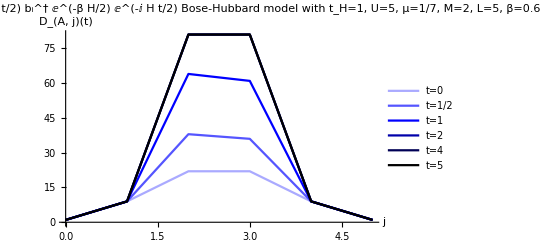

```mathematica
(* virtual bond dimension for 'A' operator *)
Partition[Import[Subscript[fn, import]<>"_DXA.dat","Integer64"],Subscript[L, val]+1]
%⟦#⟧&/@Flatten[Position[Subscript[t, list],#]&/@Subscript[t, plot]];
ListLinePlot[Transpose[{Range[0,Subscript[L, val]],#}]&/@%,AxesLabel->{"j","D_(A, j)(t)"},PlotRange->All,PlotLabel->"virtual bond dimension of ⅇ^(ⅈ H t/2) b_i^† ⅇ^(-β H/2) ⅇ^(-ⅈ H t/2)\n"<>Subscript[plot, label],PlotStyle->{Lighter[Blue,2/3],Lighter[Blue,1/3],Blue,Darker[Blue,1/3],Darker[Blue,2/3],Black},PlotLegends->("t="<>ToString[InputForm[#]]&/@Subscript[t, plot])]
Export[Subscript[fn, export]<>"DA_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]]<>".pdf",%];
```

{{1,9,22,22,9,1},{1,9,28,30,9,1},{1,9,35,40,9,1},{1,9,42,55,9,1},{1,9,58,66,9,1},{1,9,71,73,9,1},{1,9,79,78,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1}}

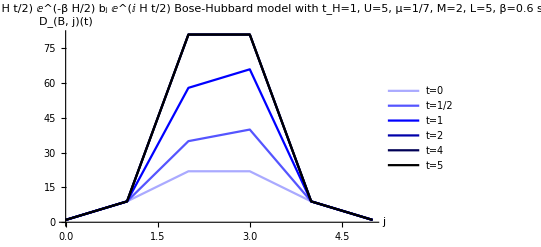

```mathematica
(* virtual bond dimension for 'B' operator *)
Partition[Import[Subscript[fn, import]<>"_DXB.dat","Integer64"],Subscript[L, val]+1]
%⟦#⟧&/@Flatten[Position[Subscript[t, list],#]&/@Subscript[t, plot]];
ListLinePlot[Transpose[{Range[0,Subscript[L, val]],#}]&/@%,AxesLabel->{"j","D_(B, j)(t)"},PlotRange->All,PlotLabel->"virtual bond dimension of ⅇ^(-ⅈ H t/2) ⅇ^(-β H/2) b_j ⅇ^(ⅈ H t/2)\n"<>Subscript[plot, label],PlotStyle->{Lighter[Blue,2/3],Lighter[Blue,1/3],Blue,Darker[Blue,1/3],Darker[Blue,2/3],Black},PlotLegends->("t="<>ToString[InputForm[#]]&/@Subscript[t, plot])]
Export[Subscript[fn, export]<>"DB_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]]<>".pdf",%];
```

### Effective truncation weight

```mathematica
(* tolerance (truncation weight) for ⅇ^(-β H/2) *)
Norm[Partition[Import[Subscript[fn, import]<>"_tol_eff_beta.dat","Real64"],Subscript[L, val]-1]-10^-10]
```

0.

```mathematica
(* tolerance (truncation weight) for ⅇ^(ⅈ H t/2) Subscript[b, i]^† ⅇ^(-β H/2) ⅇ^(-ⅈ H t/2) *)
Norm[Partition[Import[Subscript[fn, import]<>"_tol_eff_A.dat","Real64"],Subscript[L, val]-1]-10^-10]
```

0.

```mathematica
(* tolerance (truncation weight) for ⅇ^(-ⅈ H t/2) ⅇ^(-β H/2) Subscript[b, j] ⅇ^(ⅈ H t/2) *)
Norm[Partition[Import[Subscript[fn, import]<>"_tol_eff_B.dat","Real64"],Subscript[L, val]-1]-10^-10]
```

0.